# Exercise 7

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 7), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex7_Wasserman_Dan.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we are going to use the Poisson/LaPlace equation to determine the potential from a charge distribution.  We will then use our scalar electrostatic potential to determine the electric field in our system.

```mathematica
ClearAll[vxy,v1, e1, gradvxy, vxyz, gradvxyz, curlgradvxyz]
```

## Going from Charge to Electrostatic Potential

We know that a charge distribution ρ(x,y,z) and the electrostatic potential  are linked by the Poisson Equation, which tells us that the LaPlacian of the scalar electrostatic potential is equal to the (negative) charge density over the permittivity of free space: ∇^2 V=-(ρ(x,y,z))/ϵ_o .
If we think about the potential associated with a point charge at the origin, we have already determined that this can be expressed as: V(r)=Q/(4 πϵ_o|r|).  A point charge, at the origin, is a charge distribution ρ_Q=Qδ(r).  So we can see that the potential V(r) is an impulse response to the “impulse” Qδ(r).  Let’s write the potential for a point charge “Q=1/k”:

```mathematica
k=(4*Pi*8.85*10^-12)^-1
```

8.9918×10^9

```mathematica
vQ[x_,y_,z_,q_]:=k*(q/Sqrt[x^2+y^2+z^2])
```

```mathematica
Plot3D[vQ[x,y,0,1/k],{x,-1,1},{y,-1,1}, PlotRange->{0,10}]
```

-Graphics3D-

So I cut off the plot at z=10, since it clearly diverges as r->0. and I could only plot the potential in the xy plane, since we don’t know how to plot a 3D scalar function in 3D.   What about if we have a point charge at some position r’={xp,yp,zp}={1,0,0}?  This will clearly shift our potential.  How do we write this?

```mathematica
vQshift[x_,xp_,y_,yp_,z_,zp_,q_]:=k*(q/Sqrt[(x-xp)^2+(y-yp)^2+(z-zp)^2])
```

```mathematica
Plot3D[vQshift[x,1, y,0,0,0,1/k],{x,-1,1},{y,-1,1}, PlotRange->{0,10}]
```

-Graphics3D-

Plot the scalar potential for a positive charge q1=-1/k at {0,0,0} and a negative charge q2=-2/k at {1,1,1} on the xy plane:

```mathematica
Plot3D[vQshift[x,1,y,0,0,0,-2/k]+vQ[x,y,0,1/k],{x,-1,1},{y,-1,1},PlotRange->{-20,20}]
```

-Graphics3D-

We can see that the total potential is nothing more than the sums of the individual potentials arising from each point charge!  This suggests that we can find the potential from any arbitrary distribution of charge.  How?  Well, we can write:

V(r)=∫ρ(r’)k/(|r-r'|)dr'.  This means that if we have a charge distribution ρ(r’) and we want to find the potential at some point “r”, we simply integrate all of the infinitesimal potentials that come from the impulses ρδ(r’).

## Potential from distribution of point charges

Solving Poisson’s Equation in three dimensions for an arbitrary and continuous distribution of charge, using the above integral, will be tricky and require a whole lot of computational power.   Let’s try to do a piecewise expression to approximate the potential from a slab of charge.  Let’s say we have a slab of lengths Lx=1, Ly=1, and Lz=0.1, centered on the origin, with total charge qslab=1/k.   We can divide this slab into 121 point charges, each of charge dqslab=1/121k.  The potential from this charge distribution then becomes

```mathematica
Clear[vslab]
```

```mathematica
vslab[x_,y_,z_]:=Sum[(1/121)*(1/Sqrt[(x-i*.2)^2+(y-j*.2)^2+z^2]),{i,-5,5},{j,-5,5}];
```

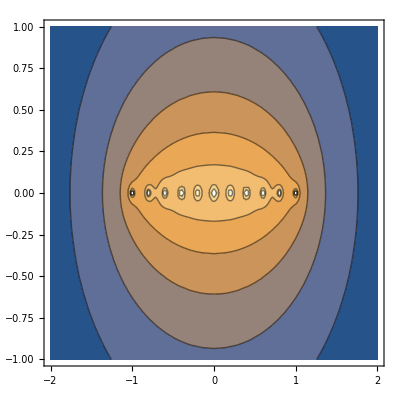

```mathematica
ContourPlot[vslab[x,0,z],{x,-2,2},{z,-1,1}]
```

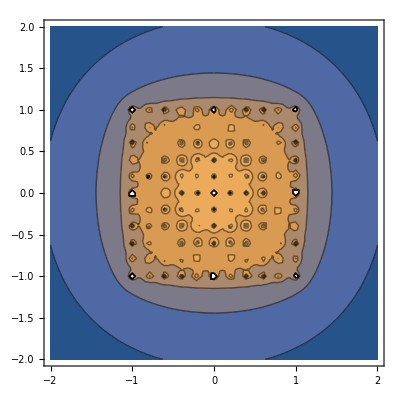

```mathematica
ContourPlot[vslab[x,y,0],{x,-2,2},{y,-2,2}]
```

This is pretty cool, but it is already starting to take quite a bit of time in Mathematica, and it is clearly still an approximation, since we can see the individual point charges we are using as approximations of a smooth charge distribution.  However, this approach isn’t inconceivable as a means of approximation.  Oftentimes we can get a really good idea of what things look like by this sort of disretization of a problem.
Of course, ultimately, Poisson and LaPlace’s equations are differential equations, and Mathematical is very good at solving these sorts of differential equations.

## Solving Poisson’s Equation using NDSolveValue

Let’s see if we can use Mathematica’s power to solve for the scalar potential given a set of boundary conditions.  There are a number of different approaches we could take, but for now, let’s see if we can simply solve for the scalar potential in the vicinity of a charged conductor.  As we learned in class, a conductor, by definition, has a uniform and singular voltage everywhere on the conductor (if it didn’t, free charge would move around to cancel out any elecric field responsible for the voltage drop).  So this means that to solve for the potential outside of a conductor (assuming it is just free space) we will use the Laplace equation.  The thing we need to be careful about, however, are boundary conditions.
To simplify, let’s start in 2D, and assume we have a charged plate, of length Lx=1, thickness Ly=0.1, centered at the origin, and held at a Voltage V=3V.

```mathematica
Ω=RegionDifference[Rectangle[{-2,-2},{2,2}],Rectangle[{-1,-0.05},{1,0.05}]]; (*Here we define the region outside of the plate*)
```

InterpolatingFunction[{{-2., 2.}, {-2., 2.}}, <>]

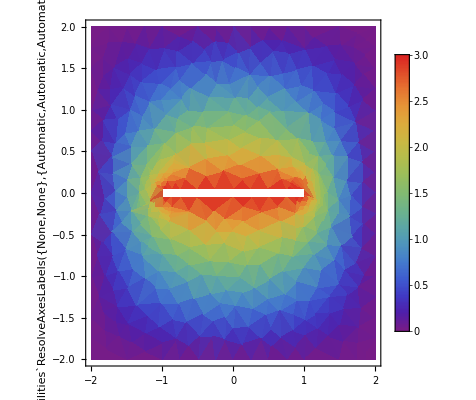

```mathematica
sol=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==0,(*This is the LaPlacian in 2D.  D is the derivative, and because we have two x's, we are telling Mathematica to take the second derivative in x*)
DirichletCondition[u[x,y]==3.,(*Here we set the boundary conditions, we tell Mathematica that sol=3 at the boundary of the conductor, defined here and in the next 4 lines*)
x==-1&&-0.05≤y≤0.05||
x==1&&-0.05≤y≤0.05||
-1≤x≤1&&y==0.05||
-1≤x≤1&&y==-0.05],
u[x,-2]==u[x,2]==u[-2,y]==u[2,y]==0},(*And here we tell Mathematica that our potential is 0 at the boundary of our region.  This is somewhat arbitrary, but if we make the region large enough, it is a good approximation*)
u,{x,y}∈Ω]  (*Here we tell mathematica to find "u", which is our potential, in the region defined by Ω*)

DensityPlot[sol[x,y],{x,y}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic]
```

So what we just did here probably requires some explanation.  The first thing I did is define the region over which we are going to apply the Laplacian.  This will be the region outside of the charged slab.  I then told Mathematica that the potential of the charged slab is V=3V, and that the potential at the boundary of our region is V=0.  These are condictions known as Dirichlet boundary conditions, and they are outside the scope of this course, so please don’t worry too much about it, unless you have extra time and are intrigued.  If you are interested, try playing around with different shapes, maybe discs or triangles...

## One-D Poisson Solver

In class we solved for the potential of a 1D system comprised of 2 slabs of charge.  Let’s see if we can use Mathematica to make this easy to do.  In 1D we can write our Poisson Equation as ⅆ^2/(ⅆ x^2)V(x)=ρ(x).  If we plug in some charge distribution, we should be able to solve for the potential.  I will solve for a single slab first, then you can solve for a 3-slab system.

```mathematica
rho1=8.85*10^-12;
```

```mathematica
rho1slab=Piecewise[{{rho1,-1≤x≤1},{0,Abs[x]>1}}]
```

Piecewise[{{8.85×10^-12, -1≤x≤1}, {0, True}}]

OK, now that we have defined our charge distribution, let’s see if you can solve for the potential.  You should be able to solve this using DSolve, which does not use a numerical technique, but solves symbolically:

```mathematica
Clear[u]
```

```mathematica
v1slab=DSolve[{D[u[x],x,x]==-rho1slab/(8.85*10^-12),u[-1]==0, u[-3]==0},u[x],x]
```

{{u[x]→Piecewise[{{0, x≤-1}, {-0.5-1. x-0.5 x^2, -1<x≤1}, {-2. x, True}}]}}

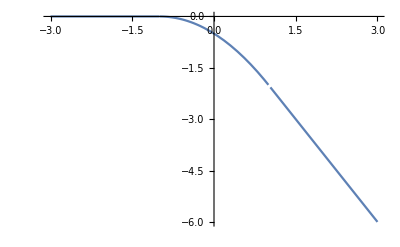

```mathematica
Plot[Evaluate[u[x]/.v1slab],{x,-3,3}]
```

So this is a little strange, why is the potential asymmetric?  It is because I told the DSolve command that our function was equal to zero at both x=-1 AND x=-3.  This is somewhat unphysical, and is not possible unless there is someother source of electric field in our system.  We know that if the slab of charge is the ONLY thing in the system, then we should have a uniform electric field on either side of our slab of charge (and therefore we would expect V(x) to have a linear dependence on x).
We can check this by finding the electric field from this charge distribution, or from the potential...

```mathematica
eslab1=-Grad[Evaluate[u[x]/.v1slab],{x,y,z}]
```

{{-(Piecewise[{{0, x<-1||x==-1}, {-1.-1. x, -1<x<1}, {-2., True}}]),0,0}}

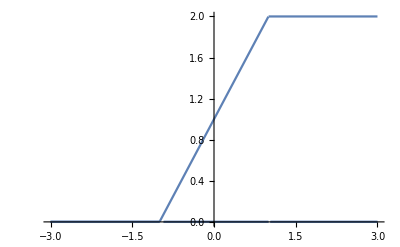

```mathematica
Plot[eslab1[[1]], {x,-3,3}]
```

Now you can try the 3 slab system, with the charge distribution below.  Calculate and plot the potential of this system of charge, assuming that the potential at x<-3 is 0.  Because this charge distribution has a net charge of 0, and is symmetric around x=0, we know, using Gauss’s law, that there should be no field outside the charge, and that therefore, the potential will be constant outside the charge.

```mathematica
rho3slab=Piecewise[{{rho1,-3≤x≤-1},{-2*rho1,-1<x<1},{rho1,1≤x≤3}},0]
```

Piecewise[{{8.85×10^-12, -3≤x≤-1}, {-1.77×10^-11, -1<x<1}, {8.85×10^-12, 1≤x≤3}, {0, True}}]

```mathematica
v2slab=DSolve[{D[u[x],x,x]==-rho3slab/(8.85*10^-12),u[-3]==0, u[-4]==0},u[x],x]
```

{{u[x]→Piecewise[{{0, x≤-3}, {-4.5-3. x-0.5 x^2, -3<x≤-1}, {-3.+1. x^2, -1<x≤1}, {-4.5+3. x-0.5 x^2, 1<x≤3}, {0, True}}]}}

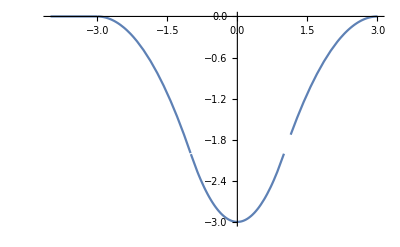

```mathematica
Plot[Evaluate[u[x]/.v2slab],{x,-4,3}]
```